# Chapter 12

## Example 12.1

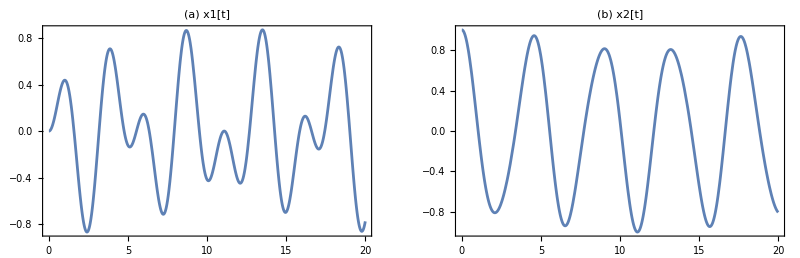

```mathematica
Remove["Global`*"]

SetOptions[Plot,BaseStyle->{FontSize->14}];

k1=4;k2=2;k3=3;m1=1;m2=2;
sol=NDSolve[{m1*x1''[t]==-k1*x1[t]+k2*(x2[t]-x1[t]),m2*x2''[t]==-k3*x2[t]+k2*(x1[t]-x2[t]),x1[0]==0,x1'[0]==0,x2[0]==1,x2'[0]==0},{x1,x2},{t,0,20}];

gr1=Plot[x1[t]/.sol,{t,0,20},PlotLabel->"(a) x1[t]"];
gr2=Plot[x2[t]/.sol,{t,0,20},PlotLabel->"(b) x2[t]"];
GraphicsGrid[{{gr1, gr2}},Frame->True]
```

## Example 12.2

{{x1[t]→a Cos[(√3 √k t)/(√m)],x2[t]→-a Cos[(√3 √k t)/(√m)]}}

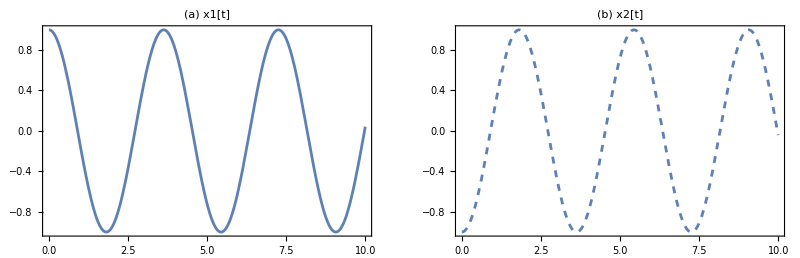

```mathematica
Remove["Global`*"]

SetOptions[Plot,BaseStyle->{FontSize->14}];

sol=ExpToTrig[DSolve[{m*x1''[t]==-k*x1[t]+k*(x2[t]-x1[t]),m*x2''[t]==-k*x2[t]+k*(x1[t]-x2[t]),x1[0]==a,x1'[0]==0,x2[0]==-a,x2'[0]==0},{x1[t],x2[t]},t]]//Simplify

numValues={a->1,k->1,m->1};

gr1=Plot[x1[t]/.sol/.numValues,{t,0,10},PlotLabel->"(a) x1[t]"];
gr2=Plot[x2[t]/.sol/.numValues,{t,0,10},PlotLabel->"(b) x2[t]",PlotStyle->Dashed];
GraphicsGrid[{{gr1, gr2}},Frame->True]
```

```mathematica
sol=ExpToTrig[DSolve[{m*x1''[t]==-k*x1[t]+k*(x2[t]-x1[t]),m*x2''[t]==-k*x2[t]+k*(x1[t]-x2[t]),x1[0]==a,x1'[0]==0,x2[0]==a,x2'[0]==0},{x1[t],x2[t]},t]]//Simplify
numValues={a->1,k->1,m->1};
```

{{x1[t]→a Cos[(√k t)/(√m)],x2[t]→a Cos[(√k t)/(√m)]}}

```mathematica
gr1=Plot[x1[t]/.sol/.numValues,{t,0,10},PlotLabel->"(c) x1[t]"];
gr2=Plot[x2[t]/.sol/.numValues,{t,0,10},PlotLabel->"(d) x2[t]",PlotStyle->Dashed];
```

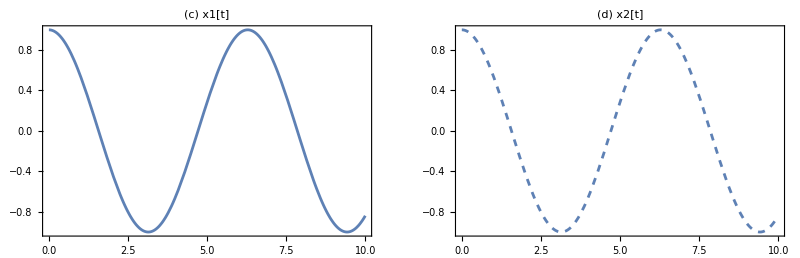

```mathematica
GraphicsGrid[{{gr1, gr2}},Frame->True]
```

## Example 12.3

{{x1[t]→1/2 a (Cos[(√k t)/(√m)]-Cos[(√3 √k t)/(√m)]),x2[t]→1/2 a (Cos[(√k t)/(√m)]+Cos[(√3 √k t)/(√m)])}}

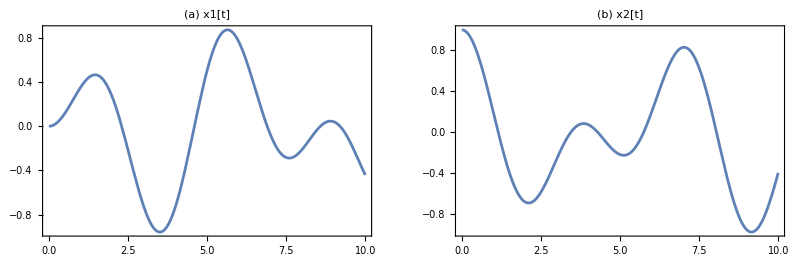

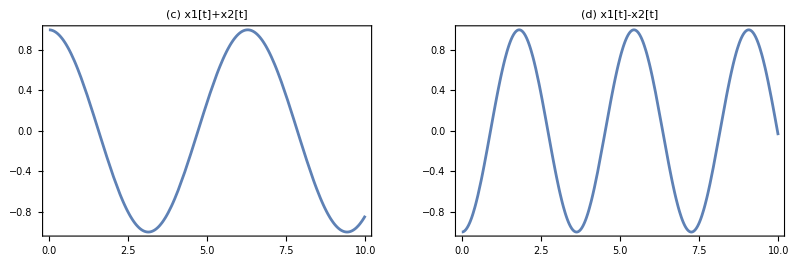

```mathematica
Remove["Global`*"]

SetOptions[Plot,BaseStyle->{FontSize->14}];

sol=ExpToTrig[DSolve[{m*x1''[t]==-k*x1[t]+k*(x2[t]-x1[t]),m*x2''[t]==-k*x2[t]+k*(x1[t]-x2[t]),x1[0]==0,x1'[0]==0,x2[0]==a,x2'[0]==0},{x1[t],x2[t]},t]]//Simplify

numValues={a->1,k->1,m->1};

gr1=Plot[x1[t]/.sol/.numValues,{t,0,10},PlotLabel->"(a) x1[t]"];
gr2=Plot[x2[t]/.sol/.numValues,{t,0,10},PlotLabel->"(b) x2[t]"];
gr3=Plot[(x1[t]+x2[t])/.sol/.numValues,{t,0,10},PlotLabel->"(c) x1[t]+x2[t]"];
gr4=Plot[(x1[t]-x2[t])/.sol/.numValues,{t,0,10},PlotLabel->"(d) x1[t]-x2[t]"];

GraphicsGrid[{{gr1, gr2}},Frame->True]
GraphicsGrid[{{gr3,gr4}},Frame->True]
```

## Example 12.4

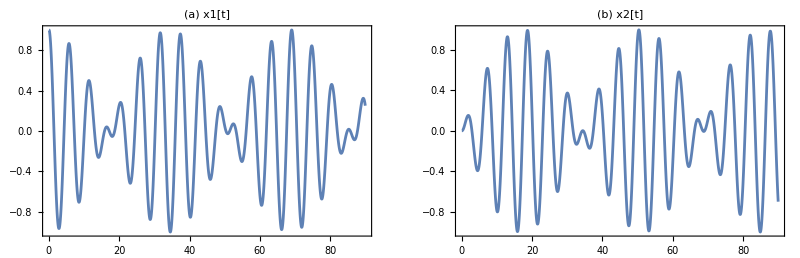

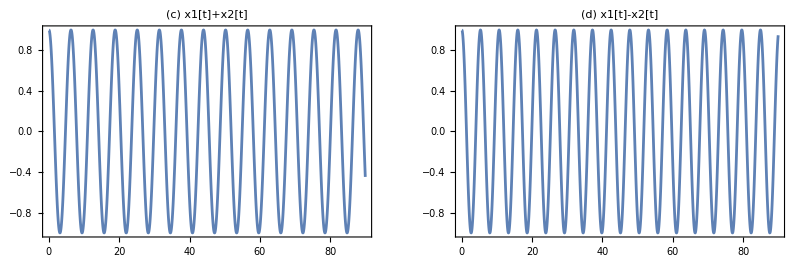

```mathematica
Remove["Global`*"]

SetOptions[Plot,BaseStyle->{FontSize->14}];

sol=ExpToTrig[DSolve[{m*x1''[t]==-k1*x1[t]+k2*(x2[t]-x1[t]),m*x2''[t]==-k3*x2[t]+k2*(x1[t]-x2[t]),x1[0]==a,x1'[0]==0,x2[0]==0,x2'[0]==0},{x1[t],x2[t]},t]]//Simplify;

numValues={a->1,k1->1,k2->.2,k3->1,m->1};

gr1=Plot[x1[t]/.sol/.numValues,{t,0,90},PlotLabel->"(a) x1[t]"];
gr2=Plot[x2[t]/.sol/.numValues,{t,0,90},PlotLabel->"(b) x2[t]"];
gr3=Plot[(x1[t]+x2[t])/.sol/.numValues,{t,0,90},PlotLabel->"(c) x1[t]+x2[t]"];
gr4=Plot[(x1[t]-x2[t])/.sol/.numValues,{t,0,90},PlotLabel->"(d) x1[t]-x2[t]"];

GraphicsGrid[{{gr1, gr2}},Frame->True]
GraphicsGrid[{{gr3,gr4}},Frame->True]
```

## Example 12.5

```mathematica
Remove["Global`*"]

x1=A1*Exp[I*ω*t];x2=A2*Exp[I*ω*t];
eq1=m*D[x1,{t,2}]+k*x1+k*(x1-x2);
expr1=(eq1)/Exp[I*ω*t]//Simplify;
Print["The first ODE yields the equation : ",expr1]
```

The first ODE yields the equation : 2 A1 k-A2 k-A1 m ω^2

```mathematica
eq2=m*D[x2,{t,2}]+k*x2+k*(x2-x1);
expr2=(eq2)/Exp[I*ω*t]//Simplify;
Print["The second ODE yields the equation : ",expr2]
```

The second ODE yields the equation : -A1 k+2 A2 k-A2 m ω^2

```mathematica
A={{Coefficient[expr1,A1],Coefficient[expr1,A2]},{Coefficient[expr2,A1],Coefficient[expr2,A2]}};
Print["The matrix A is: A = ",A]
```

The matrix A is: A = {{2 k-m ω^2,-k},{-k,2 k-m ω^2}}

```mathematica
Print["The natural frequencies are: "]
Print[Solve[Det[A]==0,ω]]
```

The natural frequencies are:

{{ω→-(√k)/(√m)},{ω→(√k)/(√m)},{ω→-(√3 √k)/(√m)},{ω→(√3 √k)/(√m)}}

## Example 12.6

```mathematica
Remove["Global`*"]

A=({{2*k/m, -k/m}, {-k/m, 2*k/m}});
Print["The frequencies are:  ",Sqrt[Eigenvalues[A]]]
```

The frequencies are:  {√3 √(k/m),√(k/m)}

```mathematica
Print["The eigenvectors are:  ",Eigenvectors[A]]
```

The eigenvectors are:  {{-1,1},{1,1}}

The eigenvectors are:  {{-1,1},{1,1}}

The eigenvectors are:  {{-1,1},{1,1}}

```mathematica
A=({{2*k/m1, -k/m1}, {-k/m2, 2*k/m2}});

rule={√(m1^2-m1 m2+m2^2)->z};
```

```mathematica
Print["The frequencies after the z-substitution are:",Sqrt[Eigenvalues[A]]/.rule]
```

The frequencies after the z-substitution are:{√((k (m1+m2-z))/(m1 m2)),√((k (m1+m2+z))/(m1 m2))}

```mathematica
Print["The eigenvectors are:", Eigenvectors[A]/.rule//Simplify]
```

The eigenvectors are:{{(m1-m2+z)/m1,1},{-(-m1+m2+z)/m1,1}}

The eigenvectors are:{{(m1-m2+z)/m1,1},{-(-m1+m2+z)/m1,1}}

The eigenvectors are:{{(m1-m2+z)/m1,1},{-(-m1+m2+z)/m1,1}}

## Example 12.7

```mathematica
Remove["Global`*"]

A=({{2*m*(-L*ω^2+g), -m*L*ω^2}, {-m*L*ω^2, -m*(L*ω^2-g)}});

Do[Print[Solve[Det[A]==({{0}, {0}}),ω][[i]]],{i,1,4}]
```

{ω→-√((2 g)/L-(√2 g)/L)}

{ω→√((2 g)/L-(√2 g)/L)}

{ω→-√((2 g)/L+(√2 g)/L)}

{ω→√((2 g)/L+(√2 g)/L)}